# 二维扩散有限元

## 缪雨轩 / Miao Yuxuan · 淮南师范学院 / Huainan Normal University

## 模型、输入与适用范围

∇⊥.b2Ez−jωμσEz=0; Jz=σEz

SI; exp(+j omega t); RMS; sigma=58 MS/m; mu_r=1; 20 C

修改 mesh_h；收敛判断至少运行三档网格。

## 推导与结果解释

在圆截面求解 ∇⊥.b2Ez−jωμσEz=0；边界常量场通过总复电流归一化。圆周多边形、插值阶次和网格尺寸共同决定数值误差。

弱形式在区域内积分 ∇v·∇Ez+jωμσvEz，并施加给定边界值。对所得电流及焦耳密度独立积分，再将 Rac 与 Bessel 解比较。

教程只用单档网格。精度判断须至少三档递减 h/a，并检查边界及圆周离散；积分守恒本身不构成场误差上界。

```mathematica
projectRoot=NestWhile[DirectoryName,NotebookDirectory[],!FileExistsQ[FileNameJoin[{#1,"pyproject.toml"}]]&&DirectoryName[#1]=!=#1&];Get[FileNameJoin[{projectRoot,"shared","wolfram","ResearchNotebook.wl"}]];
```

## 可编辑参数

```mathematica
parameters=<|"mesh_h"->0.2|>;parameters
```

<|mesh_h -> 0.2|>

## 独立进程执行与结果

```mathematica
research=LitzNotebook`RunResearch[projectRoot,"fem2",parameters];LitzNotebook`ResearchSummary[research]
```

<|run_id -> notebook_fem2_20261014005404_3f56f171, 
 
>   source_model -> 2D_circular_conductor_diffusion_FEM, 
 
>   execution_status -> completed, 
 
>   physical_acceptance_status -> passed_test_scope_only|>

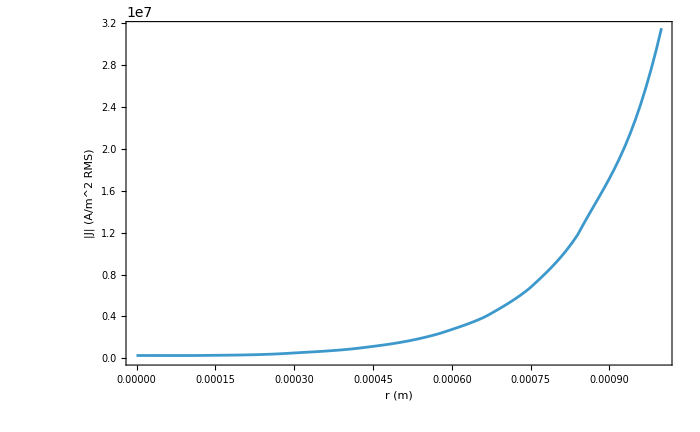

```mathematica
LitzNotebook`DisplayResearch[research]
```

## 验收与接续

核对结果中的 checks、execution_status 和 physical_acceptance_status。完整收敛与结构研究按路线 README 继续。

Sources: FEMDOC, P04; references/library.bib and references/sources.json

## 历史证据

data/evidence/v1.0.0-rc.1/; litz-research data fetch fem2